## setup

### overhead

```mathematica
(* clear all variable names and assignments *)
Clear["Global`*"];ClearAll["Global`*"];Remove["Global`*"];ClearSystemCache[];
```

```mathematica
(* directory of Mathematica files *)
dirMathematica=Environment["HOME"]<>"/Mathematica_files/";

(* ln-fhs "/Users/dantopa/Dropbox/_mm" "/Users/dantopa/Mathematica_files" *)
(* packages shared by all notebooks *)
dirnb=dirMathematica<>"nb/";
dirPack=dirnb<>"packages/";

(* seed file *)
nbSeed="seed 19_12.nb";
```

### tag

```mathematica
home="ert/mercury/snake/";  
Get["utility modules.m",Path->dirPack];
stamp1;
```

maximum memory: 1.97091 GB

seed file: /Users/dantopa/Mathematica_files/nb/seed 19_12.nb

user: dantopa, CPU: Xiuhcoatl,  MM v. 12.0.0 for Mac OS X x86

date: Apr 22, 2020, time: 22:19:09

nb: /Users/dantopa/Mathematica_files/nb/ert/mercury/snake/array-fit.nb

### modules, functions, settings, ...

#### admin

```mathematica
printmem
```

maximum memory: 1.97091 GB

```mathematica
(* save notebook *)
NotebookSave[EvaluationNotebook[]];
```

#### settings

```mathematica
exportFlag=True;
```

```mathematica
o={0,0};
```

```mathematica
guc=Circle[o,1];
```

```mathematica
ipad=ImagePadding->{{Automatic,3},{Automatic,Automatic}};
```

```mathematica
isize=ImageSize->5 72;
```

#### functions

#### substitutions

#### modules

## import

```mathematica
meanRCS=Import[dirData<>"rcs-values.dat"];
{M,𝒩}=Dimensions[meanRCS]
```

{28,361}

```mathematica
mx=Max[meanRCS]
mn=Min[meanRCS]
```

59.2522

0.798997

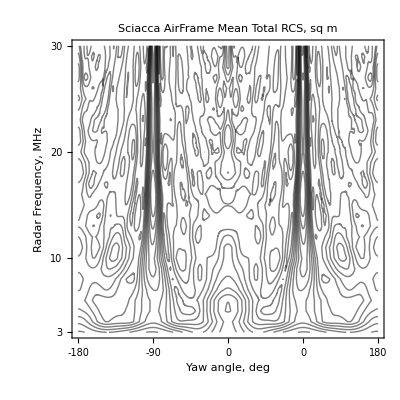

```mathematica
g000=ListContourPlot[meanRCS,
ipad,
Contours->10,
ContourShading->False,
PlotLabel->"Sciacca AirFrame"<>lf<>"Mean Total RCS, sq m",
FrameTicks->{{{{1,3},{8,10},{18,20},{28,30}},Automatic},{{{1,-180},{91,-90},{181,0},{271,0},{361,180}},Automatic}},
FrameLabel->{"Yaw angle, deg","Radar Frequency, MHz"}]
```

```mathematica
multiExport["rorschach-test",g000]
```

## 1 domain mappings

### toolkit

```mathematica
ν=Range[3,30];
```

```mathematica
{sinister,dexter}={-1,1};
```

```mathematica
Clear[linePQ];
linePQ[p_List,q_List]:=Module[{intercept,slope},
slope=(p[[2]]-q[[2]])/(p[[1]]-q[[1]]);
intercept=p[[2]]-slope p[[1]];
Return[{intercept,slope}];
]
```

### angle space

```mathematica
(* angular map *)
{left,right}={0,360};
p={left,sinister};
q={right,dexter};
```

```mathematica
linePQ[p,q]
```

{-1,1/180}

### frequency

```mathematica
(* [3, 30] ==> [-1, 1] *)
{left,right}={3,30};
p={left,sinister};
q={right,dexter};
{int,slp}=linePQ[p,q];
Print["[3,30] ==> [-1, 1]: slope = ",slp,"; intercept = ",int]
(slp #+int)&/@{3,10,20,30}
```

[3,30] ==> [-1, 1]: slope = 2/27; intercept = -11/9

{-1,-13/27,7/27,1}

```mathematica
(* [-1, 1] ==> [3, 30] *)
p={sinister,left};
q={dexter,right};
{int,slp}=linePQ[p,q];
Print["[-1, 1] ==> [3, 30]: slope = ",slp,"; intercept = ",int];
(slp #+int)&/@{-1,0,1}
```

[-1, 1] ==> [3, 30]: slope = 27/2; intercept = 33/2

{3,33/2,30}

## 2

### data vector

```mathematica
b=Flatten[meanRCS];
```

### addresses

```mathematica
Table[
{𝓍+2,𝓎-1}
,{𝓍,M},{𝓎,𝒩}];
z=Flatten[%,1]
```

{{3,0},{3,1},{3,2},{3,3},{3,4},{3,5},{3,6},{3,7},{3,8},{3,9},{3,10},{3,11},{3,12},{3,13},10081,{30,348},{30,349},{30,350},{30,351},{30,352},{30,353},{30,354},{30,355},{30,356},{30,357},{30,358},{30,359},{30,360}}
 |  |  |  |

### transform

```mathematica
z1={(2/27#[[1]]-11/9),#[[2]]}&/@z;
z2={#[[1]],((#[[2]])/180-1)}&/@z1
```

{{-1,-1},{-1,-179/180},{-1,-89/90},{-1,-59/60},{-1,-44/45},{-1,-35/36},{-1,-29/30},{-1,-173/180},{-1,-43/45},{-1,-19/20},10088,{1,19/20},{1,43/45},{1,173/180},{1,29/30},{1,35/36},{1,44/45},{1,59/60},{1,89/90},{1,179/180},{1,1}}
 |  |  |  |

```mathematica
X=z2[[All,1]];
Y=z2[[All,2]];
```

## build A

```mathematica
m=Length[X];
one=Table[1,{m}];
```

```mathematica
d=2;
Table[
Table[
{d-j,j}
,{j,0,d}]
,{d,0,7}];
powers=Flatten[%,1]
basis=(𝓍^(#[[1]])𝓎^(#[[2]]))&/@powers
```

{{0,0},{1,0},{0,1},{2,0},{1,1},{0,2},{3,0},{2,1},{1,2},{0,3},{4,0},{3,1},{2,2},{1,3},{0,4},{5,0},{4,1},{3,2},{2,3},{1,4},{0,5},{6,0},{5,1},{4,2},{3,3},{2,4},{1,5},{0,6},{7,0},{6,1},{5,2},{4,3},{3,4},{2,5},{1,6},{0,7}}

{1,𝓍,𝓎,𝓍^2,𝓍 𝓎,𝓎^2,𝓍^3,𝓍^2 𝓎,𝓍 𝓎^2,𝓎^3,𝓍^4,𝓍^3 𝓎,𝓍^2 𝓎^2,𝓍 𝓎^3,𝓎^4,𝓍^5,𝓍^4 𝓎,𝓍^3 𝓎^2,𝓍^2 𝓎^3,𝓍 𝓎^4,𝓎^5,𝓍^6,𝓍^5 𝓎,𝓍^4 𝓎^2,𝓍^3 𝓎^3,𝓍^2 𝓎^4,𝓍 𝓎^5,𝓎^6,𝓍^7,𝓍^6 𝓎,𝓍^5 𝓎^2,𝓍^4 𝓎^3,𝓍^3 𝓎^4,𝓍^2 𝓎^5,𝓍 𝓎^6,𝓎^7}

```mathematica
A={one,
one X,one Y,
X X,X Y,Y Y,
X X X,X X Y, X Y Y,Y Y Y,
X X X X,X X X Y, X X Y Y,X Y Y Y,Y Y Y Y,
X X X X X,X X X X Y,X X X Y Y,X X Y Y Y, X Y Y Y Y, Y Y Y Y Y,
X X X X X X,X X X X X Y,X X X X Y Y,X X X Y Y Y, X X Y Y Y Y, X Y Y Y Y Y,Y Y Y Y Y Y,
X X X X X X X,X X X X X X Y,X X X X X Y Y,X X X X Y Y Y,X X X Y Y Y Y,X X Y Y Y Y Y Y, X Y Y Y Y Y Y Y, Y Y Y Y Y Y Y Y}ᵀ;
Dimensions[A]
```

{10108,36}

### product matrix

```mathematica
W=A†.A;
```

```mathematica
Winv=Inverse[W];
s=SingularValueList[W];
%//N
```

{15480.3,8140.5,6587.96,3192.33,2677.52,2252.68,979.594,847.374,649.319,372.562,268.978,251.459,138.38,136.314,97.8056,50.1679,44.4061,27.9542,21.9563,17.6445,11.7717,9.69704,6.36579,4.10922,3.79086,3.1936,2.08359,1.42453,1.29534,0.997956,0.471393,0.405398,0.262634,0.124642,0.0811503,0.0399887}

### solution

```mathematica
c=LeastSquares[A,b]
```

{8.52555,5.23995,-0.229472,23.7793,-0.220598,82.0388,-69.7742,0.890601,-28.0309,0.526078,-59.7761,-0.297053,-81.607,1.43621,-147.674,144.546,-1.22258,94.2314,-1.08862,17.6838,-0.359662,51.4177,0.110074,-0.509644,0.236331,168.545,-2.55753,-19.1942,-92.6612,0.166515,-49.1343,1.35805,-39.2108,-91.0199,1.33284,97.5312}

### error

```mathematica
r=A.c-b;
```

```mathematica
r.r
```

716695.

```mathematica
σ=√((r.r)/(m-Length[c])Diagonal[Winv])
```

{0.338238,1.23409,0.873202,2.39464,2.29174,4.74676,6.98144,5.18255,4.45082,2.62758,5.58353,4.43798,7.50824,11.5813,20.6001,12.9362,10.2106,9.5018,6.08592,4.57134,2.16168,3.7247,3.26979,3.23777,3.29364,18.7461,23.4877,32.5939,7.39999,6.43353,6.31447,6.36751,6.51791,13.4443,14.2891,17.0232}

### signal-to-noise

```mathematica
sn=Abs[c]/σ
```

{25.2058,4.24602,0.262794,9.9302,0.0962578,17.2831,9.99424,0.171846,6.29792,0.200214,10.7058,0.0669343,10.869,0.124011,7.16857,11.1738,0.119737,9.91721,0.178876,3.8684,0.166381,13.8045,0.033664,0.157406,0.0717536,8.99096,0.108888,0.588889,12.5218,0.0258823,7.78122,0.213278,6.01585,6.77013,0.0932768,5.7293}

## plot

```mathematica
f[𝓍_,𝓎_]=c.basis
```

8.52555+5.23995 𝓍+23.7793 𝓍^2-69.7742 𝓍^3-59.7761 𝓍^4+144.546 𝓍^5+51.4177 𝓍^6-92.6612 𝓍^7-0.229472 𝓎-0.220598 𝓍 𝓎+0.890601 𝓍^2 𝓎-0.297053 𝓍^3 𝓎-1.22258 𝓍^4 𝓎+0.110074 𝓍^5 𝓎+0.166515 𝓍^6 𝓎+82.0388 𝓎^2-28.0309 𝓍 𝓎^2-81.607 𝓍^2 𝓎^2+94.2314 𝓍^3 𝓎^2-0.509644 𝓍^4 𝓎^2-49.1343 𝓍^5 𝓎^2+0.526078 𝓎^3+1.43621 𝓍 𝓎^3-1.08862 𝓍^2 𝓎^3+0.236331 𝓍^3 𝓎^3+1.35805 𝓍^4 𝓎^3-147.674 𝓎^4+17.6838 𝓍 𝓎^4+168.545 𝓍^2 𝓎^4-39.2108 𝓍^3 𝓎^4-0.359662 𝓎^5-2.55753 𝓍 𝓎^5-91.0199 𝓍^2 𝓎^5-19.1942 𝓎^6+1.33284 𝓍 𝓎^6+97.5312 𝓎^7

```mathematica
f[x,y]
```

8.52555+5.23995 x+23.7793 x^2-69.7742 x^3-59.7761 x^4+144.546 x^5+51.4177 x^6-92.6612 x^7-0.229472 y-0.220598 x y+0.890601 x^2 y-0.297053 x^3 y-1.22258 x^4 y+0.110074 x^5 y+0.166515 x^6 y+82.0388 y^2-28.0309 x y^2-81.607 x^2 y^2+94.2314 x^3 y^2-0.509644 x^4 y^2-49.1343 x^5 y^2+0.526078 y^3+1.43621 x y^3-1.08862 x^2 y^3+0.236331 x^3 y^3+1.35805 x^4 y^3-147.674 y^4+17.6838 x y^4+168.545 x^2 y^4-39.2108 x^3 y^4-0.359662 y^5-2.55753 x y^5-91.0199 x^2 y^5-19.1942 y^6+1.33284 x y^6+97.5312 y^7

```mathematica
ContourPlot[f[y,x],{x,-1,1},{y,-1,1},ColorFunction->(If[#1>0,Directive[Lighter[Lighter[Lighter[Yellow]]]],White]&),ColorFunctionScaling->False,
Contours->10];
```

```mathematica
ContourPlot[f[x,y],{x,-1,1},{y,-1,1},
Contours->12]
```

```mathematica
j
```

## develop

```mathematica
d=4;
Table[
{d-j,j}
,{j,0,d}]
```

{{4,0},{3,1},{2,2},{1,3},{0,4}}

```mathematica
Clear[createIndices];
createIndices[order_Integer]:=Module[{tbl},
tbl=Table[
{order-j,j}
,{j,0,order}];
Return[tbl]];
```

```mathematica
createIndices[3]
```

{{3,0},{2,1},{1,2},{0,3}}

```mathematica
indices={3,1};
column=one;
Do[
column=column X;
,{k,indices[[1]]}]
Do[
column=column Y;
,{k,indices[[2]]}]
```

```mathematica
Norm[column-X X X Y,2]
```

0

```mathematica
Clear[buildThatColumn];
buildThatColumn[howMany_List,X_List,Y_List]:=Module[{},
column=one;
(* X terms *)
Do[
column=column X;
,{k,indices[[1]]}];
(* Y terms *)
Do[
column=column Y;
,{k,indices[[2]]}];
Return[column];
]
```

```mathematica
Norm[buildThatColumn[{3,1},X,Y]-X X X Y,2]
```

0

```mathematica
Clear[buildThatSeries];
buildThatSeries[series_List,X_List,Y_List]:=Module[{},
tbl=Table[
indices=series[[k]];
buildThatColumn[indices,X,Y]
,{k,Length[series]}];
Return[tbl]
];
```

```mathematica
myIndices=createIndices[1]
```

{{1,0},{0,1}}

```mathematica
buildThatSeries[myIndices,X,Y]
tbl
```

{{-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,10002,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},1}
 |  |  |  |

{{-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,10002,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},1}
 |  |  |  |

```mathematica
Dimensions[tblᵀ]
```

{10108,2}

```mathematica
A={one};
A=AppendTo[A,tbl]
```

{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,9972,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},1}
 |  |  |  |

```mathematica
Dimensions[A]
```

{2}

```mathematica
Y
```

{-1,-179/180,-89/90,-59/60,-44/45,-35/36,-29/30,-173/180,-43/45,-19/20,-17/18,-169/180,-14/15,-167/180,-83/90,-11/12,-41/45,-163/180,-9/10,-161/180,-8/9,-53/60,-79/90,-157/180,10060,157/180,79/90,53/60,8/9,161/180,9/10,163/180,41/45,11/12,83/90,167/180,14/15,169/180,17/18,19/20,43/45,173/180,29/30,35/36,44/45,59/60,89/90,179/180,1}
 |  |  |  |

```mathematica
tbl[[1]]
```

{-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,9998,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}
 |  |  |  |

```mathematica
indices
```

{0,2}

```mathematica
buildThatColumn[{0,2},X,Y]
```

{1,32041/32400,7921/8100,3481/3600,1936/2025,1225/1296,841/900,29929/32400,1849/2025,361/400,289/324,28561/32400,196/225,27889/32400,6889/8100,121/144,10076,121/144,6889/8100,27889/32400,196/225,28561/32400,289/324,361/400,1849/2025,29929/32400,841/900,1225/1296,1936/2025,3481/3600,7921/8100,32041/32400,1}
 |  |  |  |

## end

```mathematica
(* save notebook *)
NotebookSave[EvaluationNotebook[]];
```